## Connexion DLL

## DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModel, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict];
```

### Perceptron Linéaire

#### Création modèle

```mathematica
createLinearModel = DefineDLLFunction["createLinearModel", pathToDll, "System.IntPtr", {"int", "int"}];
```

#### Classification Linéaire Rosenblatt

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "int", "double[]", "int", "int", "double"}];
```

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Régression linéaire

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Perceptron Multi - Couches

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

```mathematica
classify=DefineDLLFunction["classify",pathToDLL,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDLL,"void",{"System.IntPtr","double[]","int","int","double[]","int"}];
```

```mathematica
predict=DefineDLLFunction["predict",pathToDLL,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDLL,"void",{"System.IntPtr"}];
```

```mathematica
getOutputsforRegression=DefineDLLFunction["getOutputsforRegression",pathToDLL,"double",{"System.IntPtr"}];
```

## Cas de tests

### Simple Linéaire

```mathematica
Clear[a,b,c,positivePoints, negativePoints, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePoints = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{-1.88806,1.25618},{0.391319,1.43006},{1.62811,0.496882}}

```mathematica
negativePoints = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{4.91669,-3.04877},{-4.748,-0.762152},{-1.60019,-0.931399}}

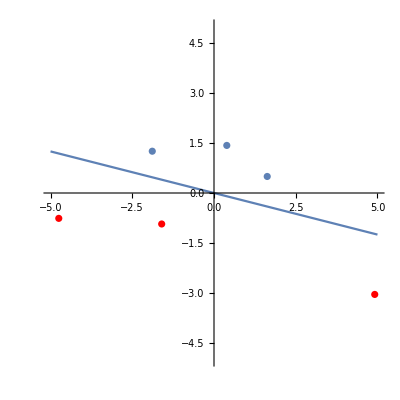

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePoints, PlotStyle->Red],
ListPlot[positivePoints]]
```

```mathematica
Clear[X, Y, model, Xtest, Ytest, Xtest2, positive, negative]
```

```mathematica
X = Flatten[{positivePoints, negativePoints}]
```

{-1.88806,1.25618,0.391319,1.43006,1.62811,0.496882,4.91669,-3.04877,-4.748,-0.762152,-1.60019,-0.931399}

```mathematica
Y = {1, 1, 1, -1, -1, -1}
```

{1,1,1,-1,-1,-1}

```mathematica
Xtest = {-4.059661874733521,3.88961785568734}
Ytest = {1}
```

{-4.05966,3.88962}

{1}

### Utilisation méthodes

```mathematica
model = createLinearModel[2,1];
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12, 2, Y, 1, 1000, 0.1];
```

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

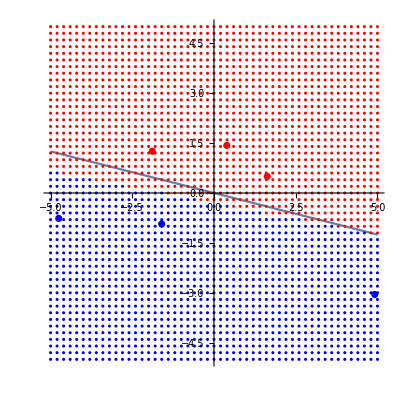

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePoints, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePoints, PlotStyle->Red, PlotStyle->Thick]]
```